Last modified on: Wednesday, July 11, 2018 at 10:44

Author Info

Jianing Lu

Matteo Salvarezza

University of Toronto

Poster Session Content

Instagram artwork classification through neural network

To classify contemporary artworks from several instagram art accounts and analyze how the images’ features relate to their popularity(number of likes and number of comments).

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

The images downloaded from several instagram accounts were classified according to their features extracted by neural network. There is a obvious visually-identifiable difference between clusters, but some deviations still remain. Features of the  most popular images appear to be very random, which is saying the relation between popularity and image features is relatively random.  Other metadata information aside from features might influence popularity greatly.

It is worth trying to make further popularity prediction on instagram posts, and analyze if other metadata information(length of captions, etc) has an important influence on popularity.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Data Collection

The data was downloaded from eight contemporary art reposting instagram accounts(to ensure the diversity of the images collected), with an instagram php scraper, making a dataset of around 9000 images. The metadata(number of likes and number of comments related to each post were also crawled.

Neural Network

Pre-trained network and self-trained network were both used. Content and style layers extracted from the “AdaIN-Style Trained on MS-COCO and Painter by Numbers Data” network, along with a pooling layer, were used. Also, a self-trained network was used. Visualization was done with and without applying cluster functions. There is an obvious visual similarity(composition of lines and colours) of the images in the same area/cluster, but deviation still remains.

{-Graphics-}

-Graphics-


-Graphics-

-Graphics-                              -Graphics-

Popularity Analysis

Through plotting images with respect to the number of likes and number of comments(after a linear correction), the distribution of  images according to popularity was achieved. After filtering out the accounts with many zero-comment but many-like posts(meaning they have a lot of fake followers giving likes but no comments ), the most popular ones seem to have random features. However, those with more number of likes tend to also have more number of comments as well, meaning some other metadata information might influence popularity greatly.

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

After applying neural network(Adain and self-trained ones), the classification result was as follows: Though there was a visually identifiable difference among clusters, many images that seemingly to belong into one genre were classified apart. In one area(before applying classification function) or cluster(after applying classification functions),  the overall colour composition and number of lines are basically the same, but it remains a question which features weigh more in obtaining the final output.
The most popular ones seem to have random features. However, those with more number of likes tend to also have more number of comments as well, meaning some other metadata information might influence popularity greatly.

#### Code

Provide one of:

https://github.com/jianinglu/wss2018

#### Written Content / Lesson Plans

#### Conclusions in Detail

Both AdaIN-Style network and self-defined one are currently insufficient for contemporary artwork classification. The difficulty lies in that contemporary art styles are very hard-to-classify themselves, and that the current neural networks have not been improved to the extent of being able to distinguish the tiny visual differences. The original data sets were not pre-labelled, and hard to be labelled by hand. If the network to use is improved to be catering more to contemporary styles classification, we’ll be provided important insights into the understanding of contemporary art. Also, as some studies suggest, image features might not be the main attributing source to social media popularity, comparing to metadata information(hashtag count, artist following, caption length, etc).

#### All Visualizations

Classification result obtained from Adain network

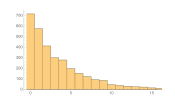
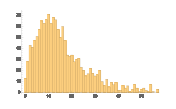
Popularity distribution after filtering out fake-follower accounts







Number of likes distribution of fake and non-fake accounts
{-Graphics-}
{-Graphics-}

Images with the most comments and likes

#### Data Sources Links/References

1. https://www.instagram.com/minute16/
2. https://www.instagram.com/painterspaintingpaintings/
3. https://www.instagram.com/artfollowers/
4. https://www.instagram.com/ppppppaint/
5. https://www.instagram.com/topainters/
6. https://www.instagram.com/abstract.mag/

#### Future Directions

It is worth trying to make further popularity prediction on instagram posts, and analyze if other metadata information(length of captions, etc) has an important influence on popularity. . On the other side, whether ideal results can ever be achieved in artwork prediction remains a questionaire.

#### Background Info Links/References

1. http://cjqian.github.io/docs/instagram_paper.pdf
2. https://arxiv.org/abs/1408.3218
3. https://arxiv.org/pdf/1505.00855.pdf

#### Keywords

< instagram >

< contemporary art >

#### Other information